```mathematica
sigmay=500000000;
b=2;
k=0.2;
Wcyc=2*(b-1)*Smax^(b+1)/(k*(b+1)*(b+2)*sigmay^(b-1));
Wf=50000000000000000000000;

Plot[Wcyc,{Smax,0,sigmay},
TicksStyle->Directive[Black,20],AxesStyle->Thick,AxesLabel->{Style["S_max",Black,24],Style["W_cyc",Black,24]},PlotStyle->{Blue,Thick},AspectRatio->0.618]
```

```mathematica
Plot[Wcyc,{Smax,0,sigmay},PlotTheme->"Scientific",TicksStyle->Directive[GrayLevel[0],20],AxesStyle->Thickness[Large],AxesLabel->{Style["\!\(\*SubscriptBox[\(S\), \(max\)]\)",GrayLevel[0],24],Style["\!\(\*SubscriptBox[\(W\), \(cyc\)]\)",GrayLevel[0],24]},PlotStyle->{RGBColor[0,0,1],Thickness[Large]},AspectRatio->0.618,AxesLabel->{Style["S_max",Black,24],Style["W_cyc",Black,24]}]
```

```mathematica
Show[%55,AxesLabel->{None,None},FrameLabel->{{HoldForm[Subscript[W, cyc]],None},{HoldForm[Subscript[S, max]],None}},PlotLabel->None,LabelStyle->{FontFamily->"Arial",13,GrayLevel[0]}]
```

```mathematica
Show[%59,ImageSize->Full]
```

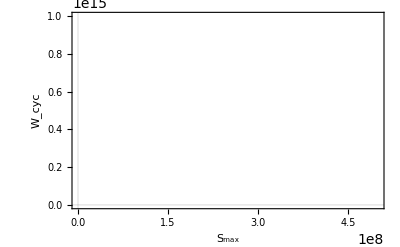

```mathematica
Show[%61,PlotLabel->None,LabelStyle->{FontFamily->"Arial",25,GrayLevel[0]}]
```